```mathematica
g=9.8; (*grav. constant*)

vt = 135; (*change this shit at will yo*)

V=439; (*given*)

θ=5*π/180; (*change this shit at will yo*)


ode1={x''[t]==(-g x'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2],y''[t]== -g (1+(y'[t]/vt^2))Sqrt[x'[t]^2+y'[t]^2],x[0]==0,x'[0]==V Cos[θ],y[0]==2,y'[0]==V Sin[θ]};
sol=NDSolve[ode1,{x,y},{t,0,200}];
```

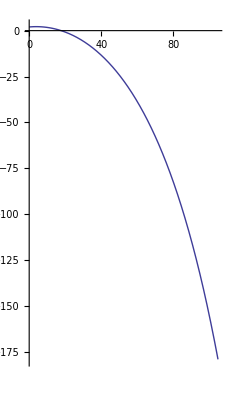

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,.25}]
```

```mathematica
Manipulate[
g=9.8;
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},{x,y}, {t, 0,200}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

NDSolve::dsfun: π/9 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(π/9),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: π/9 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(π/9),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: π/9 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(π/9),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: π/9 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(π/9),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: π/9 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(π/9),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.349066[0.000408571]], 0.349066[0.] == 0.349066, True}, 0.349066, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: π/36 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(π/36),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.0872665[0.000408571]], 0.0872665[0.] == 0.349066, True}, 0.0872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.0872665[0.000408571]], 0.0872665[0.] == 0.349066, True}, 0.0872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: π/36 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(π/36),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.0872665[0.000408571]], 0.0872665[0.] == 0.349066, True}, 0.0872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.0872665[0.000408571]], 0.0872665[0.] == 0.349066, True}, 0.0872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.